```mathematica
DS=DSolve[{p'[t]==a*p[t]-b*p[t]^2,p[0]==p0},p[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{p[t]→(a ⅇ^(a t) p0)/(a-b p0+b ⅇ^(a t) p0)}}

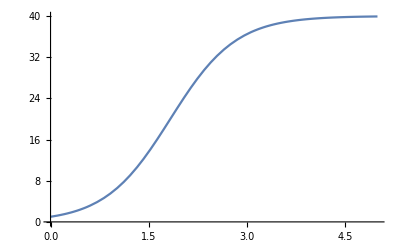

```mathematica
poput[t_]=DS[[1,1,2]];
Plot[poput[t]/.{p0->1,a->2,b->.05},{t,0,5},PlotStyle->All]
```

```mathematica
Limit[poput[t]/.{p0->1,a->2,b->.05},t->∞]
```

40.